# .7fLinear Regression by Folding

Brian Beckman
12 Feb 2018

## Motivating Example

Find best-fit, unknowns m, b, where z≈m x+b, given known data (z_1,z_2,…,z_n) and (x_1,x_2,…,x_n). Write this system as a matrix equation and remember the symbols Ζ (observations, known), A (partials, known), and Ξ (model, state, unknown parameters to be estimated). Rows of Ζ and A come in matched pairs.

Ζ_(k×1)  =  (z_1
z_2
⋮
z_k)  =  (x_1 | 1
x_2 | 1
⋮ | ⋮
x_k | 1)·(m
b) + noise  =  A_(k×2)·Ξ_(2×1)+samples of NormalDistribution[0,σ_Ζ]

This extends to any linear system with any number of parameters.7f and with tensors in the matrix slots.

Ground Truth

Make some data by sampling a line specified by the following ground truth, then adding some noise. Run the faked data through our estimation procedures and see how close the estimates come to the ground truth.

```mathematica
ClearAll[groundTruth,m,b];
groundTruth={m,b}={0.5,-1./3.};
```

Partials

The partials A are a (column) vector of co-vectors (row vectors). Each co-vector is the gradient of the observation model, namely of A·Ξ, with respect to Ξ, evaluated at a specific Ξ. Gradients of vector functions are co-vectors, that is, linear transformations of vectors. This fact becomes interesting when considering the dual problem, below.

```mathematica
ClearAll[nData,min,max];
nData=119;min=-1.;max=3.;
ClearAll[partials];
partials=Array[{#,1.0}&,nData,{min,max}];
Short[partials,3]
```

{{-1.,1.},{-0.966102,1.},{-0.932203,1.},{-0.898305,1.},«112»,{2.9322,1.},{2.9661,1.},{3.,1.}}

Fake Data

```mathematica
ClearAll[fake];
fake[n_,σ_,A_,{m_,b_}]:=
Table[
RandomVariate[NormalDistribution[0,σ]]+A⟦i⟧.{m,b},
{i,n}];
```

```mathematica
ClearAll[data,noiseSigma];
noiseSigma=0.65;
data=fake[nData,noiseSigma,partials,groundTruth];
Short[data,3]
```

{-1.06119,0.0515971,-1.31516,0.162079,«111»,1.5034,1.17977,1.76527,1.97062}

Model

Try the Wolfram built-in. The estimated m and b are reasonably close to the ground truth.

```mathematica
ClearAll[model];
model=LinearModelFit[{partials⟦All,1⟧,data}ᵀ,ξ,ξ];
Normal[model]
```

-0.28379+0.496262 ξ

Un-comment the following line to see everything Wolfram has to say about this model (it’s a lot of data).

```mathematica
(*Association[(#->model[#])&/@model["Properties"]]*)
```

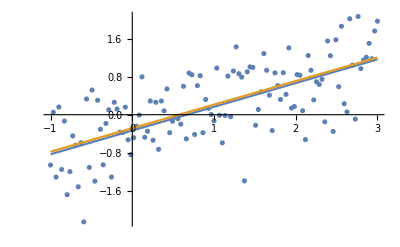

```mathematica
Show[ListPlot[{partials⟦All,1⟧,data}ᵀ],
Plot[{m ξ+b,model[ξ]},{ξ,min,max}]]
```

Normal Equations

Equation 1 can be solved for a value of Ξ that minimizes the square error J(Ξ)=^def(Ζ-A·Ξ)ᵀ·(Ζ-A·Ξ). Because the noise 𝒩(0,σ) has zero mean (or zero bias), The solution turns out to be exactly what one would get from naive algebra.  Aᵀ·A is square. When it is invertible,

(Aᵀ·A)^-1·Aᵀ·Z  =  Ξ

That gives the same answer as Wolfram’s built-in:

```mathematica
Inverse[partialsᵀ.partials].partialsᵀ.data
```

{0.496262,-0.28379}

The matrix (Aᵀ·A)^-1·Aᵀ is the Moore-Penrose left pseudoinverse. Wolfram has a built-in for it:

```mathematica
PseudoInverse[partials].data
```

{0.496262,-0.28379}

(Aᵀ·A)^-1·Aᵀ·Ζ is a very nasty computation, in memory usage, in time, and in numerical risk. Eliminate these defects with a recurrence. This recurrence is mathematically identical to a Kalman filter in parameter-estimation mode, though we do not prove that here.

## Recurrence

Fold the following recurrence over Ζ and A:

ψ←(Λ+aᵀ·a)^-1·(aᵀ·ζ+Λ·ψ)
Λ←(Λ+aᵀ·a)

where ψ is the current estimate of Ξ, a and ζ are matched rows of A and Ζ, and Λ accumulates Aᵀ·A.

Derive the recurrence as follows: Treat the estimate-so-far, ψ, as just one more observation with information matrix (proportional to inverse covariance) Λ=A_(so-far)ᵀ·A_(so-far). The scalar performance or squared error of the estimate, so far, is J(x)=(z-A_(so-far)·x)ᵀ·(z-A_(so-far)·x)=(x-ψ)ᵀ·Λ·(x-ψ), where x is the unknown true parameter vector and Λ=Aᵀ·A. Adding a new observation, ζ and its corresponding partial a, increases the error by (ζ-a·x)ᵀ·(ζ-a·x). Minimizing the new total error with respect to x yields the recurrence.

The initial value of ψ does not matter much, but the initial value of Λ cannot be singular. For practical purposes, any Λ_0 with terms much smaller than typical terms in A_(so-far)ᵀ·A_(so-far) will do. The example below starts with ψ_0=(0 | 0)ᵀ and Λ_0=((10^-6 | 0)(0 | 10^-6)).

```mathematica
ClearAll[update];
update[{ψ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{Inverse[Π].(aᵀ.ζ+ Λ.ψ),Π}];
MatrixForm/@
({({{mBar}, {bBar}}),Π}=Fold[update,
{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.496262
-0.28379),(280.356 | 119.
119. | 119.)}

The estimates mBar and bBar are exactly what we got from Wolfram’s built-in.

The mappings of List over the data and partials convert them into column vectors, as required by the recurrences in linear-algebra form.

The final value of Λ, called Π in the code, is A_full ᵀ·A_full+Λ_0

```mathematica
Π-partialsᵀ.partials
```

{{1.×10^-6,0.},{0.,1.×10^-6}}

The covariance of the estimate Ξ is ((n-1)/(n-2))*Variance[Ζ-A·Ξ]*Λ^-1 except for a small contribution from the a-priori covariance Λ_0. The correction factor ((n-1)/(n-2)) is a generalization .7fof Bessel’s correction. The 2 in (n-2) in the denominator is due to the fact that we’re estimating two parameters from the data (see VAN DE GEER, Least Squares Estimation, Volume 2, pp. 1041–1045, in Encyclopedia of Statistics in Behavioral Science, Eds. Brian S. Everitt & David C. Howell, Wiley, 2005). The denominator of the correction, in general, is n-p, where n is the number of data and p is the number of parameters being estimated.

```mathematica
Inverse[partialsᵀ.partials]*(nData-1)/(nData-2)*Variance[data-partials.{mBar,bBar}]//MatrixForm
```

(0.00236492 | -0.00236492
-0.00236492 | 0.00557159)

Except for the reversed order, this is the same covariance matrix that Wolfram reports:

```mathematica
Reverse@(Reverse/@model["CovarianceMatrix"])//MatrixForm
```

(0.00236492 | -0.00236492
-0.00236492 | 0.00557159)

Don’t Invert That Matrix.7f

See https://www.johndcook.com/blog/2010/01/19/dont-invert-that-matrix/

Replace Inverse with LinearSolve:

```mathematica
ClearAll[update];
update[{ψ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{LinearSolve[Π,(aᵀ.ζ+Λ.ψ)],Π}];
MatrixForm/@({({{mBar}, {bBar}}),Π}=Fold[update,
{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.496262
-0.28379),(280.356 | 119.
119. | 119.)}

exactly as before.

We have eliminated memory bloat by accumulating estimate updates one observation at a time, with its paired partial. We reduce computation time and numerical risk by solving a linear system instead of inverting a matrix.

## The Dual Problem

When the model is a co-vector (row-vector), e.g., a gradient, we have the dual (transposed) problem. In that case, the observations Ω and the model Γ are now.7f co-vectors with elements ω and γ  instead of ζ and ψ. The co-partials Θ (replacing A) are now a co-vector of vectors θ. The observation equation looks like Ω=Γ·Θ and the error-so-far like (x-γ)·Λ·(x-γ)ᵀ, where Λ=Θ_(so-far)·Θ_(so-far)ᵀ. We don’t change the name of Λ because it’s symmetric. Adding a new observation ω introduces new error (ω-x·θ)·(ω-x·θ)ᵀ. Minimizing the total error yields

γ←(γ·Λ+ω·θᵀ).(Λ+θ·θᵀ)^-1
Λ←(Λ+θ·θᵀ)

LinearSolve operates on the transposed right-hand side of the recurrence, and we transpose the solution to get the recurrence.

```mathematica
Transpose/@List/@partials⟦1;;3⟧
```

{{{-1.},{1.}},{{-0.966102},{1.}},{{-0.932203},{1.}}}

```mathematica
ClearAll[coUpdate];
coUpdate[{γ_,Λ_},{ω_,θ_}]:=
With[{Π=(Λ+θ.θᵀ)},
{LinearSolve[Π,Λ.γᵀ+θ.ωᵀ]ᵀ,Π}];
MatrixForm/@Fold[
coUpdate,
{({{0, 0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@List/@data,Transpose/@List/@partials}ᵀ]
```

{(0.496262 | -0.28379),(280.356 | 119.
119. | 119.)}

Application of the Dual Problem

Imagine a scalar function J(θ) of a column K-vector θ_(K×1). We want to estimate its gradient co-vector  ∇J, given a batch of ℐ random increments ΔΘ_(K×ℐ), from the system ∇J·ΔΘ=Δ J. Here, ∇J takes the role of the model whose state parameters ψ we want to estimate, ΔΘ takes the role of the partials of the model w.r.t. those parameters, and Δ J takes the role of measured data. Let Δ J_(ℐ×1) be a batch of observed increments to J and ΔΘ_(K×ℐ) be a matrix of the ℐ corresponding column-vector random increments to the input vectors θ_(K×1). The right pseudoinverse RPI=^def(ΔΘ_(K×ℐ)·ΔΘ_(K×ℐ)^ᵀ)^-1·ΔΘ_(K×ℐ)^ᵀ solves ∇ J_(ℐ×1)·ΔΘ_(K×ℐ)=Δ J_(ℐ×1) to yield ∇ J_(ℐ×1)≈Δ J_(ℐ×1)·RPI.